```mathematica
(*Problem #2a) Plot the wave equation solution with L=1, c=1, f(x)= 180x^2(1-x)
with I.C. u(x,0)=f(x) and u_t(x,0)=g(x) *)
Clear[a,b,f,x,t,n,L,g,myFSin,myFCos,c]

(*Here I define the coefficients for the terms of the series expansions*)
a[n_]:=Integrate[f[x]*Sin[n*Pi*x/L]*(2/L),{x,0,L}]
b[n_]:=Integrate[g[x]*Cos[n*Pi*x/L]*(2/(n*c*Pi)),{x,0,L}]
L=1;
c=1;

(*Below are our initial conditions when t = 0*)
f[x_]:=180*x^2*(1-x)
g[x_]:=0

Print["Coefficients"]
Simplify[a[n],Assumptions->{n>0 && n∈ Integers}]
b[n]

(*This is the definition of the solution surface*)
u[x_,t_,M_]:=Sum[a[n]*Cos[n*c*Pi*t/L]*Sin[n*Pi*x/L],{n,1,M}];

(*This definies a new function which is just first 10 terms
of the series that equals our solution surface*)
myFunction[x_,t_]:=Evaluate[u[x,t,10]]

Print["u[x,t] to 10 terms:"]
myFunction[x,t]
```

Coefficients

-(720 (1+2 (-1)^n))/(n^3 π^3)

0

u[x,t] to 10 terms:

(720 Cos[π t] Sin[π x])/π^3-(270 Cos[2 π t] Sin[2 π x])/π^3+(80 Cos[3 π t] Sin[3 π x])/(3 π^3)-(135 Cos[4 π t] Sin[4 π x])/(4 π^3)+(144 Cos[5 π t] Sin[5 π x])/(25 π^3)-(10 Cos[6 π t] Sin[6 π x])/π^3+(720 Cos[7 π t] Sin[7 π x])/(343 π^3)-(135 Cos[8 π t] Sin[8 π x])/(32 π^3)+(80 Cos[9 π t] Sin[9 π x])/(81 π^3)-(54 Cos[10 π t] Sin[10 π x])/(25 π^3)

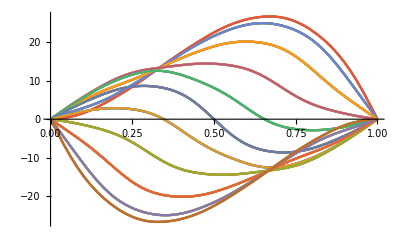

```mathematica
(*Below are the snapshots of the vibrating string at different times*)
myTable:=Table[myFunction[x,t],{t,0,5,0.1}]
Plot[myTable,{x,0,L}]
```

```mathematica
(*Here you can manipulate the plot*)
Manipulate[Plot[myFunction[x,t],{x,0,L},PlotRange->{-27,27}],{t,0,10,.05}]
```

```mathematica
Clear[t]
(*Here is the behavior over t = 0 to 2Pi of the vibrating string*)
(*From the to graphs I can conclude that that string wave is bouncing back and
forth along the entirety of the string since. This demonstrates the oscillatory nature of the vibrating string, this also shows the behavior of the vibration being UNDAMPED, the wave will continue to translate back and forth as t goes to infinity*)
Plot3D[Evaluate[myFunction[x,t]],{x,0,L},{t,0,2*Pi},BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
(*Problem #2b) Plot the wave equation solution with L=1, c=1, f(x)= 180x^2(1-x)
with I.C. u(x,0)=f(x) and u_t(x,0)=g(x) *)
Clear[a,b,f,x,t,n,L,g,myFSin,myFunction,myFCos,c]

(*Here I define the coefficients for the terms of the series expansions*)
a[n_]:=Integrate[f[x]*Sin[n*Pi*x/L]*(2/L),{x,0,L}]
b[n_]:=Integrate[g[x]*Cos[n*Pi*x/L]*(2/(n*c*Pi)),{x,0,L}]
L=Pi;
c=1;

(*Below are our initial conditions when t = 0*)
f[x_]:=2*Sin[3x]
g[x_]:=1-x

Print["Coefficients"]
Simplify[a[n],Assumptions->{n>0 && n∈ Integers}]
Simplify[b[n],Assumptions->{n>0 && n∈ Integers}]

(*This is the definition of the solution surface*)
u[x_,t_,M_]:=Sum[(a[n]*Cos[n*c*Pi*t/L]+b[n]Sin[n*c*Pi*t/L])*Sin[n*Pi*x/L],{n,1,M}];

(*This definies a new function which is just first 10 terms
of the series that equals our solution surface*)
myFunction[x_,t_]:=Evaluate[u[x,t,10]]

Print["u[x,t] to 10 terms:"]
myFunction[x,t]
```

Coefficients

0

-(2 (-1+(-1)^n))/(n^3 π)

u[x,t] to 10 terms:

(4 Sin[t] Sin[x])/π+(2 Cos[3 t]+(4 Sin[3 t])/(27 π)) Sin[3 x]+(4 Sin[5 t] Sin[5 x])/(125 π)+(4 Sin[7 t] Sin[7 x])/(343 π)+(4 Sin[9 t] Sin[9 x])/(729 π)

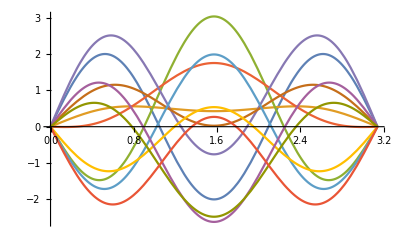

```mathematica
(*Below is a plot of the solution curves for values of t form 0 to 5 sample at 0.5 intervals*)
myTable:=Table[myFunction[x,t],{t,0,5,0.5}]
Plot[myTable,{x,0,L}]
```

```mathematica
(*Here you can manipulate the plot*)

Manipulate[Plot[myFunction[x,t],{x,0,L},PlotRange->{-3.5,3.5}],{t,0,10,0.05}]
```

```mathematica
Clear[t]
(*Here is the behavior over t = 0 to 2Pi of the vibrating string*)
(*From the to graphs I can conclude that that string wave is bouncing back and
forth along the entirety of the string since. This demonstrates the oscillatory nature of the vibrating string, this also shows the behavior of the vibration being UNDAMPED, the wave will continue to translate back and forth as t goes to infinity*)
Plot3D[Evaluate[myFunction[x,t]],{x,0,L},{t,0,2*Pi},BoxRatios->{1, 1, 1}]
```

-Graphics3D-